## This Mathematica notebook processes data from computer simulations and generates Figure S7

### Run all cells sequentially unless only a specific figure is required but in such a case please note that some previous cells must also be executed.

```mathematica
Needs["ErrorBarPlots`"]
Needs["ErrorBarLogPlots`"] (* this has to be installed separately*)
SE[x_]:=If[Length[x]>1,Sqrt[Variance[x]/Length[x]],0]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
(* a helper function which de-noises the data i.e. it removes spikes *)
Clear[DeNoise]
DeNoise[data_]:=Module[{d=data,inds={},th=0.1},
Do[
inds={};
Do[
If[Abs[d[[i-1,2]]-d[[i,2]]]>th || Abs[d[[i+1,2]]-d[[i,2]]]>th,AppendTo[inds,{i}]]
,{i,2,Length[d]-1}];
If[Length[inds]>0,d=Delete[d,inds],Break[]];
,{st,10}];
d]
```

## Fig . S7A

```mathematica
plates={{1}};
rows=8;cols=12;
dirs={NotebookDirectory[]<>"\\data_S7A"};
```

```mathematica
platedata={};
Do[
SetDirectory[dirs[[j]]];names=FileNames["*.DAT"];
names=Sort[names,(AbsoluteTime[FileDate[#1]]<AbsoluteTime[FileDate[#2]])&];
If[Length[names]==0,Interrupt[]];
Print[Length[names]];
dates=Table[AbsoluteTime[FileDate[names[[i]]]],{i,Length[names]}];
time0=AbsoluteTime[FileDate[names[[1]]]];
Monitor[
raw=Table[tmp=Import[names[[i]],"CSV"];{(dates[[i]]-time0)/3600.,tmp[[1,1]],tmp[[2;;-2]]},{i,Length[names]}],i];
Print[raw[[1,2]]];
ods=Table[Flatten[raw[[i,3]]],{i,Length[names]}];
Print[Length[ods]];
Do[If[Length[ods[[i]]]≠rows cols,Print["length error at ",i];Interrupt[]],{i,Length[names]}];
Do[AppendTo[platedata,{plates[[j,1+Mod[10000Length[plates[[j]]]+i-1-Floor[(i-1)/Length[plates[[j]]]],Length[plates[[j]]]]]],dates[[i]],ods[[i]]}],{i,Length[names]}]
,{j,Length[plates]}]
Clear[GetWell]
GetWell[pl_,line_,col_]:=Module[{ods={}},Do[If[platedata[[i,1]]==pl,AppendTo[ods,{(platedata[[i,2]]-time0)/3600.,platedata[[i,3,(line-1)cols+col]]}]],{i,Length[platedata]}];ods]
```

2962

25.2

2962

### this procedure is used to calculate growth rates :

```mathematica
Clear[FitGrowthRates,TimeToInc]
(* v1.0.x*)TimeToInc[d_]:=Module[{min=Min[d[[All,2]]],mini,max,maxi,tt=1000,thr=0.2},Do[If[d[[i,2]]==min,mini=i;max=Min[2.min+thr,Max[d[[All,2]]]];maxi=mini];
If[d[[i,2]]≥max,maxi=i;Break[]],{i,Length[d]}];
If[Max[d[[All,2]]]<min+2*thr,Return[{1000.,0.01}];];
Do[If[d[[i,2]]>min+thr,tt=0.5(d[[i,1]]+d[[i-1,1]]);Break[]],{i,mini,maxi}];{tt,0.01}
]

(* v2.1.1 *)FitGrowthRates[a1_,a2_,j_(* column = concentration *)]:=Module[{t,
tt={},mm,list={},k=1,bb,na1=0,na2=0},
Do[If[OmitWell[i,j]==False,
t=TimeToInc[GetWell[1,i,j]][[1]];
If[t>2 && t<100,
AppendTo[tt,t];
AppendTo[list,{k,k}-> If[i≤4,na1++;a1,na2++;a2]];
k++;
]];
,{i,1,8}];
If[Length[tt]≥3 && na1>0 && na2>0,
Do[AppendTo[list,{i,Length[tt]+1}->1],{i,Length[tt]}];
mm=SparseArray[list];
Print[tt];
(*Print[MatrixForm[mm]];*)
bb=1/LeastSquares[mm,tt][[1;;-2]],

bb={0,0,0,0};
];
{Conc[j],#}&/@bb
]
```

{8,8,6,6,5,5}

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

3.

{7.91236,7.96028,8.00806,8.10389,10.2574,10.2094,10.1138,10.5926}

{8.72569,8.67778,8.39111,8.34319,10.5447,11.0231,11.4533,11.4533}

{29.2815,43.3697,28.7092,28.375,78.7425,74.7786,33.4347,39.7386}

{{{0,0.682449},ErrorBar[0.0239381]},{{2,0.635511},ErrorBar[0.0222908]},{{4,0.171346},ErrorBar[0.0251157]},{{5,0},ErrorBar[0]},{{6,0},ErrorBar[0]},{{8,0},ErrorBar[0]}}

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

3.

{9.34819,9.53944,9.39611,9.49167,12.4097,13.4139,12.9354,12.4575}

{9.44389,9.53944,9.53944,9.10875,12.6486,12.6486,12.9354,12.6008}

{9.44389,9.53944,9.63514,9.2525,12.6964,12.6008,12.7919,12.7442}

{9.58722,9.58722,9.58722,9.68306,12.1228,12.8875,12.6964}

{9.68306,9.58722,9.53944,9.44389,12.6964,12.9354,12.9354,12.7919}

{9.2525,9.68306,9.82667,9.68306,12.9354,12.4575,12.5053,12.6964}

{{{0,0.560331},ErrorBar[0.0132388]},{{2,0.563383},ErrorBar[0.0125627]},{{4,0.561769},ErrorBar[0.0130083]},{{5,0.540316},ErrorBar[0.0196376]},{{6,0.555985},ErrorBar[0.0126339]},{{8,0.560313},ErrorBar[0.0167377]}}

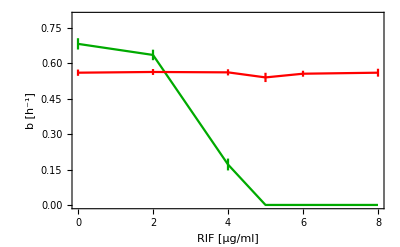

```mathematica
Clear[OmitWell,Conc]
Clear[MeanCurve]
MeanCurve[d_]:={{Mean[#[[All,1]]],Mean[#[[All,2]]]},ErrorBar[SE[#[[All,2]]]]}&/@Gather[d,#1[[1]]==#2[[1]]&]
except={{7,5},{7,6}};
OmitWell[row_,col_]:=If[Position[except,{row,col}]≠{},True,False];
Conc[j_]:={8,8,6,6,5,5,4,4,2,2,0,0}[[j]];
Table[Conc[j],{j,6}]
mut1=MeanCurve[Module[{a1,a2,a},a1=(a/.FindMinimum[Variance[FitGrowthRates[a,a+Log[10],1][[All,2]]],{a,3.}][[2]]);Print[a1];a2=a1+Log[10];Flatten[Table[FitGrowthRates[a1,a2,j],{j,11,1,-2}],1]]]
mut2=MeanCurve[Module[{a1,a2,a},a1=(a/.FindMinimum[Variance[FitGrowthRates[a,a+Log[10],1][[All,2]]],{a,3.}][[2]]);Print[a1];a2=a1+Log[10];Flatten[Table[FitGrowthRates[a1,a2,j],{j,12,1,-2}],1]]]

ErrorListPlot[{mut1,mut2},PlotRange->{0,0.8},BaseStyle->{FontSize->24},PlotStyle->{Darker[Green],Red},Joined->True,Frame->True,FrameLabel->{"RIF [μg/ml]","b [h^-1]"},ImageSize->{Automatic,250},FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}}]
```

## Fig. S7B

### this imports the plate reader data and creates a time series:

```mathematica
plates={{1}};
rows=8;cols=12;
dirs={NotebookDirectory[]<>"\\data_S7B"};
```

```mathematica
platedata={};
Do[
SetDirectory[dirs[[j]]];names=FileNames["*.DAT"];
names=Sort[names,(AbsoluteTime[FileDate[#1]]<AbsoluteTime[FileDate[#2]])&];
If[Length[names]==0,Interrupt[]];
Print[Length[names]];
dates=Table[AbsoluteTime[FileDate[names[[i]]]],{i,Length[names]}];
time0=AbsoluteTime[FileDate[names[[1]]]];
Monitor[
raw=Table[tmp=Import[names[[i]],"CSV"];{(dates[[i]]-time0)/3600.,tmp[[1,1]],tmp[[2;;-2]]},{i,Length[names]}],i];
Print[raw[[1,2]]];
ods=Table[Flatten[raw[[i,3]]],{i,Length[names]}];
Print[Length[ods]];
Do[If[Length[ods[[i]]]≠rows cols,Print["length error at ",i];Interrupt[]],{i,Length[names]}];
Do[AppendTo[platedata,{plates[[j,1+Mod[10000Length[plates[[j]]]+i-1-Floor[(i-1)/Length[plates[[j]]]],Length[plates[[j]]]]]],dates[[i]],ods[[i]]}],{i,Length[names]}]
,{j,Length[plates]}]
Clear[GetWell]
GetWell[pl_,line_,col_]:=Module[{ods={}},Do[If[platedata[[i,1]]==pl,AppendTo[ods,{(platedata[[i,2]]-time0)/3600.,platedata[[i,3,(line-1)cols+col]]}]],{i,Length[platedata]}];ods]
```

1402

23.8

1402

### this procedure is used to calculate growth rates :

```mathematica
Clear[FitGrowthRatesGlobal]
(* v3.1 *)FitGrowthRatesGlobal[j_]:=Module[{t,tt={},tt1={},tt2={},mm,list={},k=1,bb,rates={}},
Do[If[OmitWell[i,j]==False,t=TimeToInc[GetWell[1,i,j]]⟦1⟧;If[t>2&&t<100,AppendTo[tt,t];If[i≤4,AppendTo[tt1,t],AppendTo[tt2,t]];AppendTo[list,{k,1}->If[i≤4,0,Log[10]]];k++;]];,{i,1,8}];
(*Print[tt];*)If[Length[tt1]≥2 && Length[tt2]≥2,Do[AppendTo[list,{i,2}->1],{i,Length[tt]}];mm=SparseArray[list];
(*Print[MatrixForm[mm]];*)Do[bb=1/(LeastSquares[Delete[mm,n],Delete[tt,n]]⟦1⟧);AppendTo[rates,bb],{n,Length[tt]}],rates={0};];(*Print[bb];*)
{{Conc[j],Mean[rates]},ErrorBar[Sqrt[Variance[rates]Length[tt]/(Length[tt]-1)]]}]
```

### GFP strain :

{0.,1.75,2.625,3.5,5.25,7.}

Variance::shlen: The argument {0} should have at least two elements.

{{{0.,0.951139},ErrorBar[0.0115316]},{{1.75,0.892454},ErrorBar[0.0119686]},{{2.625,0.71544},ErrorBar[0.0118176]},{{3.5,0.409732},ErrorBar[0.0187448]},{{5.25,0},ErrorBar[√2 √Variance[{0}]]},{{7.,0},ErrorBar[√2 √Variance[{0}]]}}

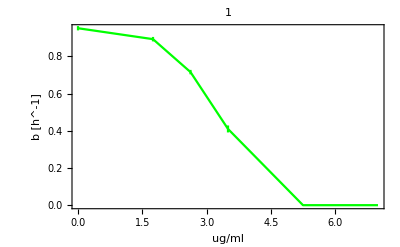

```mathematica
Clear[OmitWell,Conc]
Clear[MeanCurve]
MeanCurve[d_]:={{Mean[#[[All,1]]],Mean[#[[All,2]]]},ErrorBar[SE[#[[All,2]]]]}&/@Gather[d,#1[[1]]==#2[[1]]&]
except={{1,5},{2,5},{3,5},{4,5},{1,6},{2,6},{3,6},{4,6}};
OmitWell[row_,col_]:=If[Position[except,{row,col}]≠{},True,False];
Conc[j_]:={0.,1.75,2.625,3.5,5.25,7.,0.,1.75,2.625,3.5,5.25,7.}[[j]];
Table[Conc[j],{j,6}]
mut1=Table[FitGrowthRatesGlobal[i],{i,6}]
ErrorListPlot[mut1,PlotStyle->Green,Joined->True,Frame->True,FrameLabel->{"ug/ml","b [h^-1]"},PlotLabel->"1"]
```

### mKate strain:

{0.,1.75,2.625,3.5,5.25,7.}

Variance::shlen: The argument {0} should have at least two elements.

{{{0.,0.943478},ErrorBar[0.0105651]},{{1.75,0.79368},ErrorBar[0.028686]},{{2.625,0.642038},ErrorBar[0.00489618]},{{3.5,0.341061},ErrorBar[0.0121845]},{{5.25,0},ErrorBar[√2 √Variance[{0}]]},{{7.,0},ErrorBar[√2 √Variance[{0}]]}}

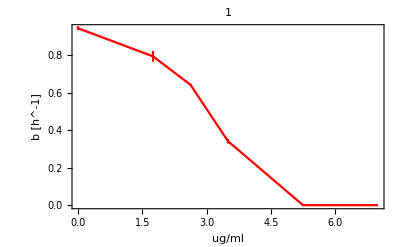

```mathematica
except={{1,11},{2,11},{3,11},{4,11},{1,12},{2,12},{3,12},{4,12}};
OmitWell[row_,col_]:=If[Position[except,{row,col}]≠{},True,False];
Table[Conc[j],{j,7,12}]
mut2=Table[FitGrowthRatesGlobal[i],{i,7,12}]
ErrorListPlot[mut2,PlotStyle->Red,Joined->True,Frame->True,FrameLabel->{"ug/ml","b [h^-1]"},PlotLabel->"1"]
```

### final figure :

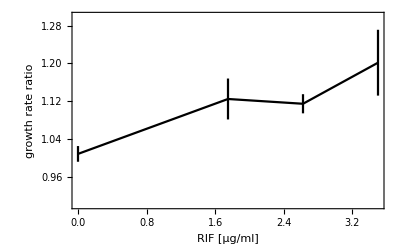

```mathematica
ErrorListPlot[Table[{{Conc[i],x/y},ErrorBar[Sqrt[dx^2/y^2+dy^2 x^2/y^4]]}/.{x->mut1[[i,1,2]],y->mut2[[i,1,2]],dx->mut1[[i,2,1]],dy->mut2[[i,2,1]]},{i,4}],PlotRange->{0.9,1.3},BaseStyle->{FontSize->24},PlotStyle->{Black},Joined->True,Frame->True,FrameLabel->{"RIF [μg/ml]","growth rate ratio"},ImageSize->{Automatic,250},FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}}]
```